# SDR4MR script.nb Lecture et analyse fichier WAV créé par une radio logicielle et un logiciel, CubicSDR ici. -Graphics- HSJ 04/07/2024 V2 11/07/2024 : quelques corrections, améliorations. d’après ReadWav SDR 1. fichier 2. lecture => data 3. Visualisation partielle 4. Analyse fréquentielle permet une bonne estimation de la fréquence de démodulation à appliquer en 5. 5. Visualisation détaillée (R/I, phase, module) filtrage passe-bas et démodulation complémentaire. 6. Graphique R, I, module

```mathematica
nnb=Last@FileNameSplit@NotebookFileName[];
version="1.1";
verbeux=False;
```

```mathematica
SetOptions[$FrontEndSession,DockedCells->Cell[BoxData[ToBoxes[nnb<>" "<>version<>" sélection du fichier .WAV, analyses temporelles et fréquencielles, démodulation numérique",StandardForm]],"DockedCells",ShowStringCharacters->False,CellMargins->{{0,0},{0,0}},Background->Orange]]
```

## 1. Sélection du fichier .wav ici fichier exemple:

```mathematica
fichier="C:\\Users\\HSJ\\Documents\\EN_COURS\\Publis\\RF Monitor\\MAGMA\\Documents pour Magma\\63.640_2024-12-02_15-16-43.wav"
```

C:\Users\HSJ\Documents\EN_COURS\Publis\RF Monitor\MAGMA\Documents pour Magma\63.640_2024-12-02_15-16-43.wav

## 2. Lecture fichier => data Variables : tEch : période d’échantillonnage en secondes nbPoints : nombre de points (paire de points) date : date heure d’enregistrement du fichier Avec la radio logicielle RTL SDR & CubicSDR : fichier Wav avec 2 octets par point.

```mathematica
data=Import[ fichier,"Data"];
nbPoints=Dimensions[data][[2]];
Print["Nombre de paires de points ; "<>ToString[nbPoints]]
tEch=1/Import[fichier,"SampleRate"];
Print["Période d'échantillonnage : "<>ToString[N[tEch 10^6]]<> " microsecondes"]
Print["Durée enregistrée : "<>ToString[N[tEch nbPoints]]<> " secondes"]
date=StringTake[fichier,-23]
Print["Valeur maximum (si 1 => saturation) : "<>ToString[Max[data]]]
```

Nombre de paires de points ; 1657729

Période d'échantillonnage : 5.20833 microsecondes

Durée enregistrée : 8.63401 secondes

2024-12-02_15-16-43.wav

Valeur maximum (si 1 => saturation) : 0.926145

## 3. Visualisation partielle Affichage sous-échantillonné de la totalité du fichier (maximum maxAff 3000000 points ou duréeMaxAff secondes).

```mathematica
maxAff=300000;
duréeMaxAff=maxAff tEch;
sousEchant= Ceiling[nbPoints/maxAff];
tt1=Take[data[[1]],{1,-1,sousEchant}];
tt2=Take[data[[2]],{1,-1,sousEchant}];
nbPointsSousE=Dimensions[tt1][[1]]
d1=1; f1=nbPointsSousE;
If[f1> nbPointsSousE|| d1>f1,d1=1;f1=nbPointsSousE,rien];
df=" Visualisation R I 1/"<>ToString[sousEchant]<>" points\nenregistrement : "<>ToString[date]<>" \nSous-échantillons, début : "<>ToString[d1]<>", fin : "<>ToString[f1];
ListPlot[{tt1[[d1;;f1]],tt2[[d1;;f1]]}, PlotRange->All, PlotLabel->df]
dPar=Abs[Transpose[{tt1[[d1;;f1]], tt2[[d1;;f1]]}].{1,I}];
cutoff=10000;dParLP=LowpassFilter[dPar,  cutoff 2 π,SampleRate-> 1/tEch];
cutoffH=0;
dParLPH=HighpassFilter[dParLP,  cutoffH 2 π,SampleRate-> 1/tEch];
temps=Range[f1-d1+1]tEch sousEchant;
ListPlot[Transpose[{temps,dParLPH}], PlotRange->All, AxesLabel->{"Temps (s)", "RF(ua)"}, PlotLabel->"Visualisation du module"]
```

276289

-Graphics-

-Graphics-

## 4. Analyse fréquentielle (ici temps en secondes) Dans cet exemple, deux répétitions complètes de 50 à 650 ms => capture d’écran -Graphics-

```mathematica
ok=False;
ok=True
deb=1;
If[ok,Manipulate[ 
duréeTotale=N[tEch nbPoints];
pasDurée=N[Round[100duréeTotale]/1000];
débutP=Max[Round[débutSecondes /tEch],1];
deltaVisu=Round[duréeObs/tEch]; 
finP=débutP+  deltaVisu;
If[finP > nbPoints,finP=nbPoints,rien];
If[débutP >= nbPoints|| débutP>=finP,débutP=1,rien];
(* *)

(*coupure en Hz désormais;*);
dPar=Abs[Transpose[{data[[1]][[débutP;;finP]], data[[2]][[débutP;;finP]]}].{1,I}];
riPar={data[[1]][[débutP;;finP]],data[[2]][[débutP;;finP]]};
Δts=N[tEch];
longueurP=finP-débutP+1;
ΔfHz=1/(longueurP Δts);
tfHz=Table[((ii-1)-Round[longueurP/2])ΔfHz,{ii,1,longueurP}];
tF=Abs[Fourier[(Transpose[riPar].{1,I})]];
tF=RotateLeft[tF, Round[longueurP/2]];

df=" enregistrement RI : "<>ToString[date]<>" \ndébut : "<>ToString[débutP]<>", fin : "<>ToString[finP]<>"\n début (ms) : "<>ToString[Round[N[1000 débutP tEch]]]<>", fin (ms): "<>ToString[Round[N[1000 (finP)tEch]]]<>"\n Δt affiché (ms) : "<>ToString[Round[N[1000 (longueurP)tEch]]];
fa="Max : "<>ToString[Max[tF]]<>", fréquence Hz: "<>ToString[(Flatten[FindPeaks[tF,1,0,Max[tF]/2]][[1]] )ΔfHz+tfHz[[1]]];
GraphicsColumn[{ListPlot[TimeSeries[LowpassFilter[dPar,  freqCoupure 2 π,SampleRate-> 1/tEch],{0 tEch, (longueurP-1) tEch}], PlotRange->All,AxesLabel->{"t(s)",RF B1},AxesStyle->{Directive[Red,12],Blue},PlotLabel->df,GridLines->Automatic], 
ListPlot[Transpose[{tfHz,tF}],PlotRange->{{-ftDf,ftDf},{0,ftAmp}},AxesLabel->{"f(Hz)",RF B1},AxesStyle->{Directive[Red,12],Blue}, PlotLabel->fa,GridLines->Automatic, Joined->True]}],{débutSecondes,0, duréeTotale,pasDurée},{{duréeObs,N[Round[1000duréeMaxAff/4]/1000]},0,duréeMaxAff,0.01},{{freqCoupure,10000},1000,1/(tEch 2),1000},{{ftAmp,5},0.5,10,1},{{ftDf,100000},10000,100000,10000},TrackedSymbols:>{débutSecondes,duréeObs,freqCoupure, ftAmp,ftDf},ContinuousAction->False],rien]
```

True

## 5. Visualisation détaillée attention on reprend le fichier complet et on regarde de début à longueur. seuilT = seuil sur l’amplitude temporelle pour le calcul de la phase Toutes les fréquences ci-dessous sont en Hz Filtre passe-bas : fCoupureT (sur signal temporel) Démodulation : la démodulation permet de décaler la fréquence du signal (=fIRM-fOscillateur local Radio logicielle) par exemple pour la ramener à 0 avec : fDemod (quelques 10 kHz), vernierfDemod (petites variations). Attention : -en 2D multicoupes la fréquence des impulsions fIRM change beaucoup d’une coupe à l’autre, -Attention : la démodulation est appliquée à partir du temps initial. phase0 : un décalage de phase peut être appliquée au signal pour mieux le visualiser. Analyse des impulsions successives : -Graphics- 1. STIR -Graphics- -Graphics- 2. Excitation de l’eau -Graphics- 3. Pi -Graphics-

```mathematica
débutP=.;
longueurP=.;
Manipulate[
seuilT=0.01;
maxVisu=Min[maxAff,nbPoints-1];
If[débutP+longueurP> nbPoints,débutP=nbPoints-longueurP-1,rien];
If[longueurP>maxVisu,longueurP=maxVisu,rien];df=" enregistrement RI : "<>ToString[date]<>" \ndébut : "<>ToString[débutP]<>", fin : "<>ToString[débutP+longueurP]<>"\n début (ms) : "<>ToString[Round[N[1000 débutP tEch]]]<>", fin (ms): "<>ToString[Round[N[1000 (débutP+longueurP)tEch]]]<>"\n Δt affiché (ms) : "<>ToString[Round[N[1000 (longueurP)tEch]]]<>"\n fDémod (Hz) : "<>ToString[fDemod + vernierfDemod];
pR="Partie réelle";
pI="Partie imaginaire";
pPhase=" phase (°): ";
pMod=" module  ";
temps=Range[longueurP+1]tEch;
dParDt=Transpose[{data[[1]][[débutP;;débutP+longueurP]],data[[2]][[débutP;;débutP+longueurP]]}];
dParD=dParDt.{1,I} Exp[I (2 π  (fDemod + vernierfDemod)temps + phase0 π/180)];

dParD=LowpassFilter[dParD,  fCoupureT 2 π,SampleRate-> 1/tEch] ;

dParM=Abs[dParD];
unZero=Threshold[dParM,seuilT];
dParP=LowpassFilter[Arg[dParD],  fCoupureT 2 π,SampleRate-> 1/tEch] unZero;

GraphicsGrid[{{Graphics[Text[Style[df,Blue,Italic,12]]],SpanFromLeft},{ListPlot[{N[Re[dParD]]}, Joined->True,PlotRange->All, PlotLabel->pR,PlotStyle->Red],ListPlot[{N[Im[dParD]]}, Joined->True,PlotRange->All, PlotLabel->pI]},
{ListPlot[{N[180 dParP/π]}, Joined->True,PlotRange->All, PlotLabel->pPhase],
ListPlot[{N[dParM]}, Joined->True,PlotRange->All, PlotLabel->pMod]}
}, Frame->All],Row[{Control[{{débutP,1, "début (points)"},1,nbPoints,500,ControlPlacement->Bottom}],Control[{{longueurP,Round[maxVisu/2],"longueur (points)"},1,maxVisu,1000,ControlPlacement->Bottom}]}],Row[{Control[{{fCoupureT,30000, "Filtre PB (Hz)"},500,70000,1000,ControlPlacement->Bottom}],Control[{{phase0,0, "Phase en°"},-180,180,2,ControlPlacement->Bottom}]}],Row[{Control[{{fDemod,0,"F démodulation (Hz)"},-30000,20000,1000,ControlPlacement->Bottom}],Control[{{vernierfDemod,0,"ΔF démodulation (Hz)"},-100,100,0.5,ControlPlacement->Bottom}]}],
ControlPlacement->{Bottom,Bottom,Bottom,Bottom},TrackedSymbols:>{débutP,longueurP,fCoupureT, phase0,fDemod,vernierfDemod},Method->{"ControlAreaDisplayFunction"->(Pane[#1,ImageSize->Automatic,ImageSizeAction->"ResizeToFit",AppearanceElements->{"ResizeArea"}]&)},ContinuousAction->False]
```

## Graphique de la dernière impulsion observée au §5 (R, I, module) dec : permet de centrer l’impulsion (axe des temps) PlotRange→{{-8,8},{-0.4,0.8}} => ajustement du graphique

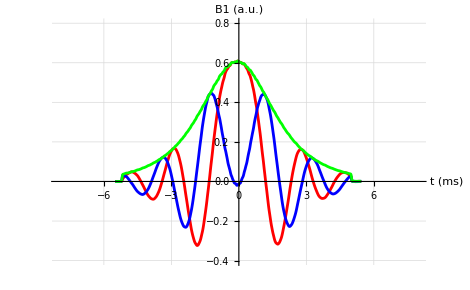

```mathematica
ms=1000;np=Length[dParD];
dec=-0.0055;
tax=Table[dec+ ii tEch,{ii,1,np}] ms;ListPlot[{Transpose[{tax,N[Re[dParD]]}],Transpose[{tax,N[Im[dParD]]}],Transpose[{tax,N[dParM]}]}, Joined->True,GridLines->Automatic,PlotStyle->{Red,Blue, Green},AxesStyle->{{14,Bold},{14,Bold}},PlotRange->{{-8,8},{-0.4,0.8}},AxesLabel->{" t (ms)","B1 (a.u.)"},LabelStyle->Directive[Black,Bold]]
```